```mathematica
r=3000;
vIn = 10;
c = 100 10^-9;
```

### Frequency Response in Low-Pass Arrangement

```mathematica
vOutLowPass[f_]:=vIn (1/(2 Pi f c))/Sqrt[r^2+(1/(2 Pi f c))^2]
```

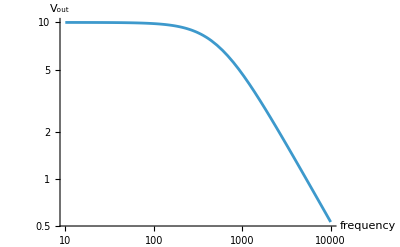

```mathematica
LogLogPlot[vOutLowPass[f],{f,10, 10000}, GridLines->Automatic, AxesLabel->{"frequency","V_out"}]
```

### Frequency Response in High-Pass Arrangement

```mathematica
vOutHighPass[f_]:=vIn r/Sqrt[r^2+(1/(2 Pi f c))^2]
```

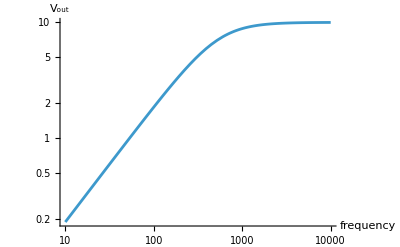

```mathematica
LogLogPlot[vOutHighPass[f],{f,10, 10000}, GridLines->Automatic, AxesLabel->{"frequency","V_out"}]
```